```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.4,Jtwo,0.4,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.36514837167011066}]
```

{z→0.365148}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.4,l->0.4}
```

0.365148+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.36514837167011066]]
```

{{0.005,0.37608},{0.01,0.386581},{0.015,0.396679},{0.02,0.406394},{0.025,0.415747},{0.03,0.424751},{0.035,0.433421},{0.04,0.441766},{0.045,0.449796},{0.05,0.457516},{0.055,0.464931},{0.06,0.472046},{0.065,0.478862},{0.07,0.485381},{0.075,0.491603},{0.08,0.497527},{0.085,0.503153},{0.09,0.508476},{0.095,0.513496},{0.1,0.518209}}

```mathematica
moduler[Lister[-1,-0.005,0.36514837167011066]]
```

{{-0.005,0.353754},{-0.01,0.341858},{-0.015,0.329415},{-0.02,0.316365},{-0.025,0.302639},{-0.03,0.288147},{-0.035,0.272773},{-0.04,0.256365},{-0.045,0.238718},{-0.05,0.219539},{-0.055,0.198392},{-0.06,0.174571},{-0.065,0.146788},{-0.07,0.112146},{-0.075,0.0597273},{-0.08,-0.240122},{-0.085,-0.240203},{-0.09,-0.240127},{-0.095,-0.240437},{-0.1,-0.240748}}

```mathematica
{{-0.005,0.3537539182557586},{-0.01,0.3418582622203128},{-0.015,0.3294145502870945},{-0.02,0.3163653589410917},{-0.025,0.30263944982321717},{-0.03,0.2881470728553941},{-0.035,0.27277293774126105},{-0.04,0.2563652657506737},{-0.045,0.23871787043422685},{-0.05,0.21953893356367007},{-0.055,0.1983919539313645},{-0.06,0.17457079356808466},{-0.065,0.1467876817436544},{-0.07,0.11214583653343176},{-0.075,0.05972725862177993},{-0.08,-0.24012172832910417},{-0.085,-0.24020342505403652},{-0.09,-0.24012711772983933},{-0.095,-0.24043715810693855},{-0.1,-0.24074777776229067}}
```

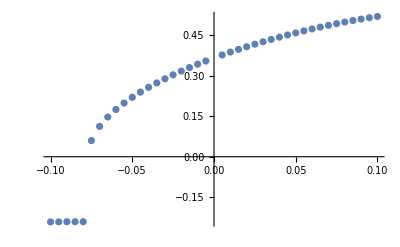

```mathematica
ListPlot[{{0.005,0.3760802101956303},{0.01,0.3865814323597306},{0.015,0.39667869196216266},{0.02,0.4063942385972723},{0.025,0.41574663984085763},{0.03,0.4247513438698238},{0.035,0.4334211237913019},{0.04,0.44176643330567483},{0.045,0.44979569541162406},{0.05,0.45751554038816944},{0.055,0.464931005443647},{0.06,0.47204570567482623},{0.065,0.4788619839856866},{0.07,0.48538104612627503},{0.075,0.4916030858705241},{0.08,0.49752740442781246},{0.085,0.5031525273915853},{0.09,0.5084763218015912},{0.095,0.5134961151864673},{0.1,0.5182088177292198},{-0.005,0.3537539182557586},{-0.01,0.3418582622203128},{-0.015,0.3294145502870945},{-0.02,0.3163653589410917},{-0.025,0.30263944982321717},{-0.03,0.2881470728553941},{-0.035,0.27277293774126105},{-0.04,0.2563652657506737},{-0.045,0.23871787043422685},{-0.05,0.21953893356367007},{-0.055,0.1983919539313645},{-0.06,0.17457079356808466},{-0.065,0.1467876817436544},{-0.07,0.11214583653343176},{-0.075,0.05972725862177993},{-0.08,-0.24012172832910417},{-0.085,-0.24020342505403652},{-0.09,-0.24012711772983933},{-0.095,-0.24043715810693855},{-0.1,-0.24074777776229067}}]
```

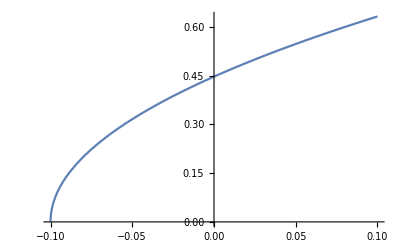

```mathematica
Plot[Sqrt[1+2*(0.4*Cos[Inv[0.4,Jtwo]]+Jtwo*Cos[2*Inv[0.4,Jtwo]])],{Jtwo,-0.1,0.1}]
```